#1 Perfect plasticity

```mathematica
Subscript[σ, Y]=3*10^8;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
N[ep]
```

0.00142857

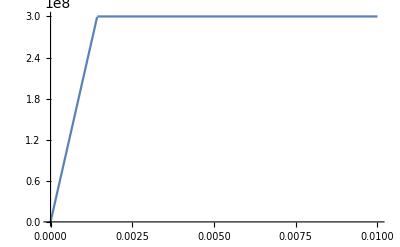

```mathematica
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[σ, Y], x>ep}}]
Plot[sigma[x],{x,0,0.01}]
```

#2 Isotropic hardening (linear)

```mathematica
??Global`*
```

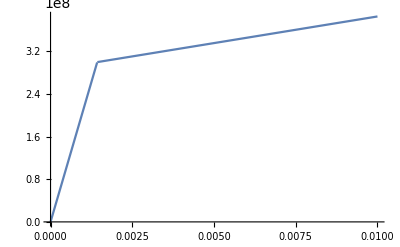

```mathematica
Subscript[σ, Y]=3*10^8;
K=1*10^10;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
Subscript[K, 1][α_]:=Subscript[σ, Y]+K α;
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[K, 1][x-ep], x>ep}}]
Plot[sigma[x],{x,0,0.01},AxesOrigin->{0,0}]
```

```mathematica
Grid[Table[{i,Subscript[K, 1][i]},{i,0,0.004,0.0005}]]
```

0. | 3.*^8
0.0005 | 3.05*^8
0.001 | 3.1*^8
0.0015 | 3.15*^8
0.002 | 3.2*^8
0.0025 | 3.25*^8
0.003 | 3.3*^8
0.0035 | 3.35*^8
0.004 | 3.4*^8

#3 Alternative isotropic hardening (exponential)

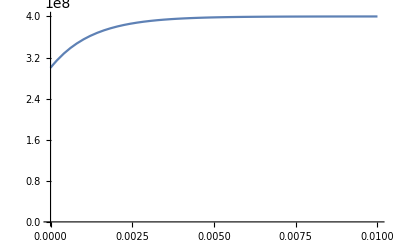

```mathematica
Subscript[σ, Y]=3*10^8;
K=1*10^8; 
H=0;
θ=1;
δ=800;
Subscript[K, 2][α_]:=Subscript[σ, Y]+θ H α+K(1-Exp[-δ α]);
Plot[Subscript[K, 2][x],{x,0,10*10^(-3)},AxesOrigin->{0,0}]
```

```mathematica
Grid[Table[{Subscript[K, 2][i],i},{i,0,0.01,0.0002}]]
```

3.×10^8 | 0.
3.14786×10^8 | 0.0002
3.27385×10^8 | 0.0004
3.38122×10^8 | 0.0006
3.47271×10^8 | 0.0008
3.55067×10^8 | 0.001
3.61711×10^8 | 0.0012
3.67372×10^8 | 0.0014
3.72196×10^8 | 0.0016
3.76307×10^8 | 0.0018
3.7981×10^8 | 0.002
3.82796×10^8 | 0.0022
3.85339×10^8 | 0.0024
3.87507×10^8 | 0.0026
3.89354×10^8 | 0.0028
3.90928×10^8 | 0.003
3.9227×10^8 | 0.0032
3.93413×10^8 | 0.0034
3.94387×10^8 | 0.0036
3.95217×10^8 | 0.0038
3.95924×10^8 | 0.004
3.96526×10^8 | 0.0042
3.9704×10^8 | 0.0044
3.97478×10^8 | 0.0046
3.97851×10^8 | 0.0048
3.98168×10^8 | 0.005
3.98439×10^8 | 0.0052
3.9867×10^8 | 0.0054
3.98867×10^8 | 0.0056
3.99034×10^8 | 0.0058
3.99177×10^8 | 0.006
3.99299×10^8 | 0.0062
3.99402×10^8 | 0.0064
3.99491×10^8 | 0.0066
3.99566×10^8 | 0.0068
3.9963×10^8 | 0.007
3.99685×10^8 | 0.0072
3.99731×10^8 | 0.0074
3.99771×10^8 | 0.0076
3.99805×10^8 | 0.0078
3.99834×10^8 | 0.008
3.99858×10^8 | 0.0082
3.99879×10^8 | 0.0084
3.99897×10^8 | 0.0086
3.99912×10^8 | 0.0088
3.99925×10^8 | 0.009
3.99936×10^8 | 0.0092
3.99946×10^8 | 0.0094
3.99954×10^8 | 0.0096
3.99961×10^8 | 0.0098
3.99966×10^8 | 0.01

#4 Kinematic hardening